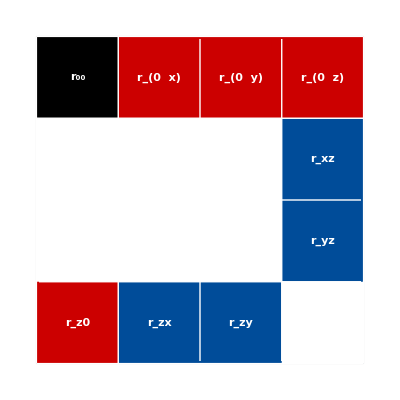

```mathematica
Graphics[{{White,EdgeForm[Directive[Black,Thick]],Rectangle[{0,1},{4,-3}]},
{Black,EdgeForm[Directive[White,Thick]],Rectangle[{0,0},{1,1}]},{RGBColor["#CC0000"],EdgeForm[Directive[White,Thick]],Rectangle[{1,0},{4,1}]},{RGBColor["#CC0000"],EdgeForm[Directive[White,Thick]],Rectangle[{0,0},{1,-3}]},
{RGBColor["#004C99"],EdgeForm[Directive[White,Thick]],Rectangle[{1,0},{4,-3}]},
{White,Text[Style["r_00",Bold,Large],{0.5,0.5}]},
{White,Text[Style["r_(0  x)",Bold,Large],{1.5,0.5}]},
{White,Text[Style["r_(0  y)",Bold,Large],{2.5,0.5}]},
{White,Text[Style["r_(0  z)",Bold,Large],{3.5,0.5}]},
{White,Text[Style["r_x0",Bold,Large],{0.5,-0.5}]},
{White,Text[Style["r_y0",Bold,Large],{0.5,-1.5}]},
{White,Text[Style["r_z0",Bold,Large],{0.5,-2.5}]},
{White,Text[Style["r_xx",Bold,Large],{1.5,-0.5}]},
{White,Text[Style["r_xy",Bold,Large],{2.5,-0.5}]},
{White,Text[Style["r_xz",Bold,Large],{3.5,-0.5}]},
{White,Text[Style["r_yx",Bold,Large],{1.5,-1.5}]},
{White,Text[Style["r_yy",Bold,Large],{2.5,-1.5}]},
{White,Text[Style["r_yz",Bold,Large],{3.5,-1.5}]},
{White,Text[Style["r_zx",Bold,Large],{1.5,-2.5}]},
{White,Text[Style["r_zy",Bold,Large],{2.5,-2.5}]},
{White,Text[Style["r_zz",Bold,Large],{3.5,-2.5}]},
{White,Rectangle[{0,0},{3,-2}]},
White,Rectangle[{3,-2},{4,-3}],
Directive[White,Thick],Line[{{2,0.97},{2,-2.97}}],
White,Thick,Line[{{3,0.97},{3,-2.97}}],
White,Thick,Line[{{0.03,-1},{3.97,-1}}],
White,Thick,Line[{{0.03,-2},{3.97,-2}}]},Frame->None
]
```

```mathematica
Graphics[{Black,Rectangle[{0,0},{1,-1}],
RGBColor["#CC0000"],Rectangle[{0,-1},{1,-4}],
White,Text[Style["r_0",Bold,Large],{0.5,-0.5}],
White,Text[Style["r_x",Bold,Large],{0.5,-1.5}],
White,Text[Style["r_y",Bold,Large],{0.5,-2.5}],
White,Text[Style["r_z",Bold,Large],{0.5,-3.5}],
White,Thick,Line[{{0,-1},{1,-1}}],
White,Thick,Line[{{0,-2},{1,-2}}],
White,Thick,Line[{{0,-3},{1,-3}}]}]
```

-Graphics-

```mathematica
Graphics3D[{Black,Cuboid[{-0.5,-0.5,-0.5},{0.5,0.5,0.5}],
RGBColor["#CC0000"],Cuboid[{-0.5,0.5,0.5},{0.5,3.5,-0.5}],
RGBColor["#CC0000"],Cuboid[{0.5,-0.5,0.5},{3.5,0.5,-0.5}],
RGBColor["#CC0000"],Cuboid[{0.5,0.5,0.5},{-0.5,-0.5,3.5}],
RGBColor["#004C99"],Cuboid[{0.5,0.5,0.5},{-0.5,3.5,3.5}],
RGBColor["#004C99"],Cuboid[{0.5,0.5,0.5},{3.5,-0.5,3.5}],
RGBColor["#004C99"],Cuboid[{0.5,0.5,0.5},{3.5,3.5,-0.5}],
RGBColor["#99FF33"],Cuboid[{0.5,0.5,0.5},{3.5,3.5,3.5}]},Axes->False,AxesLabel->{x,y,z},LabelStyle->Directive[Bold, Large,White],PlotRange->{{-0.5,3.5},{-0.5,3.5},{-0.5,3.5}},AxesOrigin->{0.5,0.5,0.5},AxesStyle->Thickness[0.01]]
```

-Graphics3D-

```mathematica
Solve[n^3==3.5(36+12n+n^2),n]//FullSimplify
```

{{n→-2.94833-2.17171 ⅈ},{n→-2.94833+2.17171 ⅈ},{n→9.39667}}

```mathematica
SparseArray[{{1,4},{3,6},{5,2}}->{a,b,c},{6,6}]//Normal//MatrixForm
```

(0 | 0 | 0 | a | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | b
0 | 0 | 0 | 0 | 0 | 0
0 | c | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)